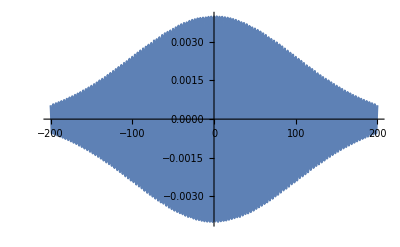

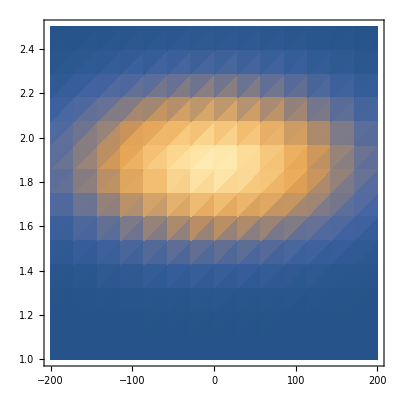

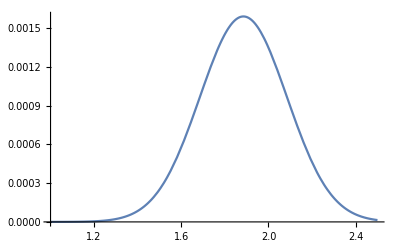

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

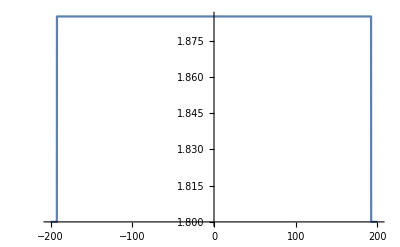

```mathematica
Clear["Global`*"]
(*Constants*)(*um,fs*)
c=0.3;
(*refractive index for BK7; *)
n[λ_]:=√(1+(1.03961212 λ^2)/(λ^2−0.00600069867)+(0.231792344 λ^2)/(λ^2-0.0200179144)+(1.01046945 λ^2)/(λ^2-103.560653));

(*Gaussian pulse*)
pulseWidth = 100; 
centralWavelength = 1 ;
centralω=2π c/centralWavelength;
pulse[t_] :=1/(pulseWidth √(2π))Exp[-t^2/(2 pulseWidth^2)]Exp[-ⅈ(2π c)/centralWavelength t];
Plot[Re[pulse[t]],{t,-200,200}]
(*Check instaneous spectrum with central t and width w*)
windowWidth = 5;
instantSpectrum[t_,ω_]:=Abs[FourierTransform[pulse[tt]*1/(windowWidth √(2π))Exp[-(tt-t)^2/(2 windowWidth^2)],tt,ω]];
(*spectrum (color vs y) as a function of time x*)
DensityPlot[instantSpectrum[t,ω],{t,-200,200},{ω,1,2.5},PlotRange->Full]
(*A sclice of density plot*)
Plot[instantSpectrum[0,ω],{ω,1,2.5},PlotRange->Full]
(*peak frequency as a function of time*)
Plot[FindMaximum[instantSpectrum[t,ω],{ω,1.8}]⟦2,1,2⟧,{t,-200,200},PlotRange->Full]
```

```mathematica
(*
From Louradour_Kalashyan_2012_OptExp, assume Subscript[A, 1] Subscript[B, 1] and Subscript[B, 1] Subscript[C, 1] are both 0.
-Graphics--Graphics-
*)
(*refractive angle out of the first grism*)
θ5[α_,d_,θ_,ω_]:=ArcSin[n[(2π c)/ω]Sin[π/2-α-ArcSin[Sin[α-ArcSin[Sin[θ]/n[(2π c)/ω]]]-(2π c)/(ω d)]]];
c1c2[α_,d_,θ_,dd_,ω_]:=dd/Cos[θ5[α,d,θ,ω]];
xp=1;(*this is an arbitrary constant, Subscript[A, 2] Subscript[T, 2]*)
(*length of Subscript[C, 2] Subscript[B, 2] plus Subscript[B, 2] Subscript[A, 2]*)
(*cba[α_,d_,θ_,dd_,ω_]:=(xp Sin[α])/Cos[ArcSin[Sin[α-ArcSin[Sin[θ]/n[ω]]]-(2π c)/(ω d)]]+(xp Cos[π/2-α-ArcSin[Sin[α-ArcSin[Sin[θ]/n[ω]]]-(2π c)/(ω d)]])/Cos[ArcSin[Sin[α-ArcSin[Sin[θ]/n[ω]]]-(2π c)/(ω d)]] Sin[α]/Cos[ArcSin[Sin[θ]/n[ω]]];*)
cba[α_,d_,θ_,dd_,ω_]:=(xp Sin[α] (√(1-Sin[θ]^2/n[(2π c)/ω]^2)+Sin[α-ArcSin[(2 c π)/(d ω)+Cos[α+ArcSec[Csc[θ] n[(2π c)/ω]]]]]))/(√(1-(2 c π+d ω Cos[α+ArcSec[Csc[θ] n[(2π c)/ω]]])^2/(d^2 ω^2)) √(1-Sin[θ]^2/n[(2π c)/ω]^2));
(*length of Subscript[A, 2] Subscript[I, 2]*)
(*ai2[α_,d_,θ_,dd_,ω_]:=(xp Cos[π/2-α-ArcSin[Sin[α-ArcSin[Sin[θ]/n[ω]]]-(2π c)/(ω d)]])/Cos[ArcSin[Sin[α-ArcSin[Sin[θ]/n[ω]]]-(2π c)/(ω d)]] Cos[α-ArcSin[Sin[θ]/n[ω]]]/Cos[ArcSin[Sin[θ]/n[ω]]];*)
ai2[α_,d_,θ_,dd_,ω_]:=-((xp Cos[α+ArcCos[(2 c π)/(d ω)+Cos[α+ArcSec[Csc[θ] n[(2π c)/ω]]]]] Sin[α+ArcSec[Csc[θ] n[(2π c)/ω]]])/(√(1-(2 c π+d ω Cos[α+ArcSec[Csc[θ] n[(2π c)/ω]]])^2/(d^2 ω^2)) √(1-Sin[θ]^2/n[(2π c)/ω]^2)));

tg[α_,d_,θ_,dd_,ω_]:=2/c(n[(2π c)/ω](cba[α,d,θ,dd,ω])+c1c2[α,d,θ,dd,ω]-ai2[α,d,θ,dd,ω]);
(*just a test: tg[π/6,10,0,10000,0.3*2π]*)
```

149488.

-Graphics-

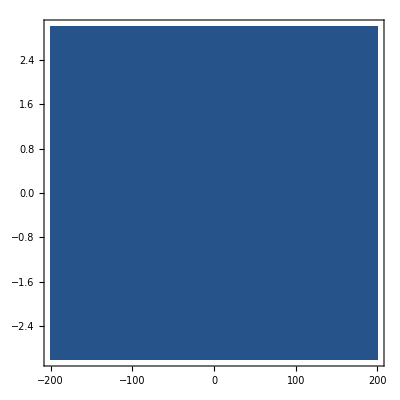

```mathematica
(*Just an experiment*)
fPulse[ω_]:=FourierTransform[pulse[t],t,ω];
shiftedPulse[t_]:=InverseFourierTransform[fPulse[ω](*Exp[ⅈ 0.01 ω^2]*),ω,t];
Plot[Re[shiftedPulse[t]],{t,-200,200}]
instantSpectrum[t_,ω_]:=Abs[FourierTransform[shiftedPulse[tt]*1/(windowWidth √(2π))Exp[-(tt-t)^2/(2 windowWidth^2)],tt,ω]];
(*spectrum (color vs y) as a function of time x*)
DensityPlot[instantSpectrum[t,ω],{t,-200,200},{ω,-3,3},PlotRange->Full]
(*Plot[Abs[fPulse[ω]],{ω,-2,2},PlotRange->Full]*)
```

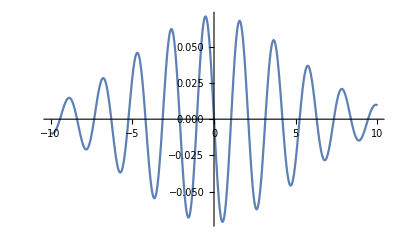

General::munfl: Exp[-1012.44+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

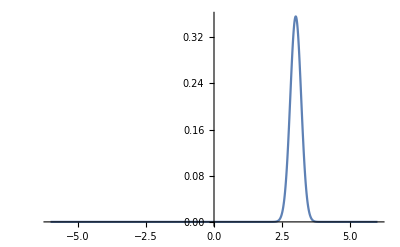

-Graphics-

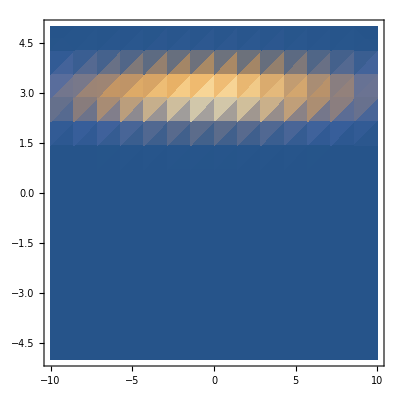

```mathematica
(*another test*)
(*Clear["Global`*"];*)
k = 3;σ=5;windowWidth=5;
F[x_]:=Exp[-ⅈ k x] 1/(2π √σ)Exp[-x^2/(2 σ^2)];
Plot[Im[F[x]],{x,-10,10}]
fF[kk_]:=FourierTransform[F[x],x,kk];
Plot[Abs[fF[kk]],{kk,-6,6},PlotRange->All]
sF[x_]:=InverseFourierTransform[fF[kk],kk,x];
Plot[Im[sF[x]],{x,-10,10}]

instantSpectrum[t_,ω_]:=Abs[FourierTransform[sF[tt]*1/(windowWidth √(2π))Exp[-(tt-t)^2/(2windowWidth)],tt,ω]];
(*spectrum (color vs y) as a function of time x*)
DensityPlot[instantSpectrum[t,ω],{t,-10,10},{ω,-5,5},PlotRange->Full]
```